```mathematica
Factor[z^3+2 z^2-4z-8]
```

(-2+z) (2+z)^2

```mathematica
A = ({{0, 1, 0}, {0, 0, 1}, {8, 4, -2}})
```

{{0,1,0},{0,0,1},{8,4,-2}}

```mathematica
Eigensystem[A]
```

{{-2,-2,2},{{1,-2,4},{0,0,0},{1,2,4}}}

```mathematica
JordanDecomposition[A]//MatrixForm
```

((1
1
1) | (-2
-1
2) | (4
0
4)
(-2
1
0) | (0
-2
0) | (0
0
2))

```mathematica
Det[A - λ IdentityMatrix[3]]
```

8+4 λ-2 λ^2-λ^3

## 3.

```mathematica
Y1 = Un;
Y2 = Un + 1/2 k λ Un;
Y3 = Un +1/2 k λ (Un + 1/2 k λ Un);
Y4 = Un + k λ(Un +1/2 k λ (Un + 1/2 k λ Un));
Un1 = Un + 1/6 k λ(Un + 2(Un + 1/2 k λ Un) + 2(Un +1/2 k λ (Un + 1/2 k λ Un)) + Un + k λ(Un +1/2 k λ (Un + 1/2 k λ Un)))//FullSimplify//Expand
```

Un+k Un λ+1/2 k^2 Un λ^2+1/6 k^3 Un λ^3+1/24 k^4 Un λ^4

```mathematica
Y1 = Un;
Y2 = Un + 1/2 k λ Y1;
Y3 = Un +1/2 k λ (Y2);
Y4 = Un + k λ(Y3);
Un1 = Un + 1/6 k λ(Y1 + 2(Y2) + 2(Y3) +Y4)//FullSimplify//Expand
```

Un+k Un λ+1/2 k^2 Un λ^2+1/6 k^3 Un λ^3+1/24 k^4 Un λ^4

```mathematica
(1 + k λ + 1/2(k λ)^2 + 1/6(k λ)^3 + 1/24(k λ)^4)Un
```

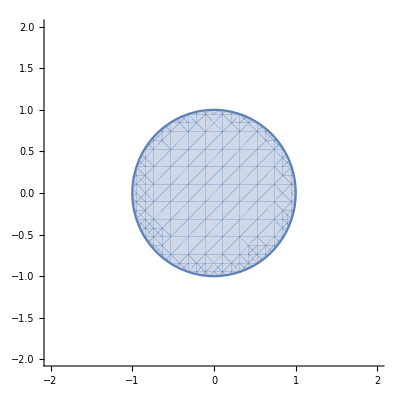

```mathematica
p[z_]:=1 + z + 1/2 z^2 + 1/6 z^3 + 1/24 z^4
RegionPlot[Abs[x + ⅈ y]≤1,{x,-2,2},{y,-2,2},Axes->True,Frame->False]
```